```mathematica
Integrate[x Sin[x*r]/(1+x^2/Λ^2),{x,0,Infinity}]
Integrate[x Exp[-x^2/Λ^2]*Sin[x*r],{x,0,Infinity}]
```

ConditionalExpression[(ⅇ^(-Abs[r]/(√(1/Λ^2))) π r Λ^2)/(2 Abs[r]), r∈ℝ&&(Re[Λ^2]≥0||Λ^2∉ℝ)]

ConditionalExpression[(ⅇ^(-1/4 r^2 Λ^2) √π r)/(4 (1/Λ^2)^(3/2)), Re[Λ^2]>0]

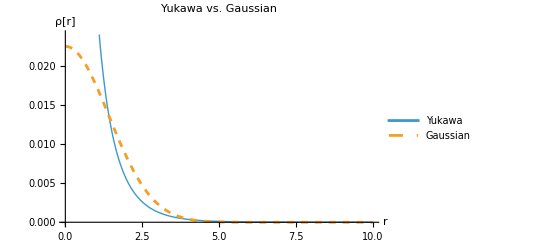

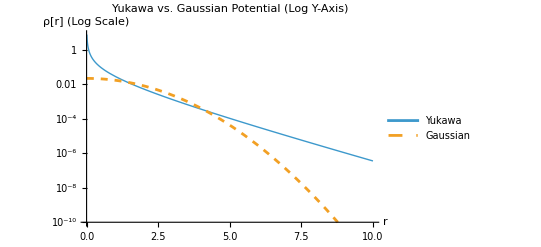

```mathematica
F1[r_]:=1/(2Pi^2r)(ⅇ^(-(√(r^2))/(√(1/Λ^2))) π r Λ^2)/(2 √(r^2)) /. Λ->1
F2[r_]:=1/(2Pi^2r) (ⅇ^(-1/4 r^2 Λ^2) √π r)/(4 (1/Λ^2)^(3/2))/. Λ->1
Plot[{F1[r],F2[r]},{r,0.01,10},PlotLegends->{"Yukawa","Gaussian"},PlotStyle->{Thick,Dashed},AxesLabel->{"r","ρ[r]"},PlotLabel->"Yukawa vs. Gaussian" ]
Plot[{F1[r],F2[r]},{r,0.01,10},PlotLegends->{"Yukawa","Gaussian"},PlotStyle->{Thick,Dashed},AxesLabel->{"r","ρ[r] (Log Scale)"},PlotLabel->"Yukawa vs. Gaussian Potential (Log Y-Axis)",(*新增此行以設定 Y 軸為對數尺度*)ScalingFunctions->"Log",(*確保 PlotRange 的下限是正數，以便進行對數計算*)
PlotRange->{10^(-10),All}]
```

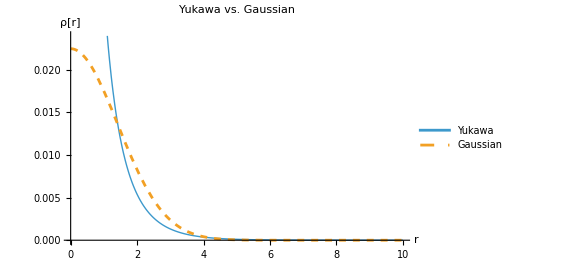

-Graphics-

(0.0031831 ⅇ^(-0.2 √(r^2)))/(√(r^2))

0.000179587 ⅇ^(-0.01 r^2)

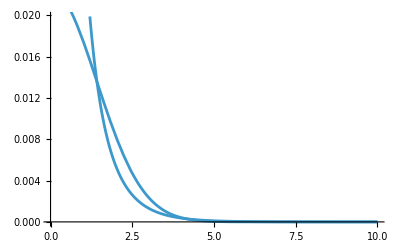

```mathematica
F1[r]
F2[r]
```